MAJ3

```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

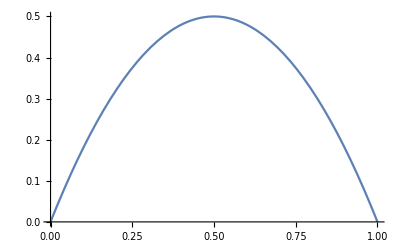

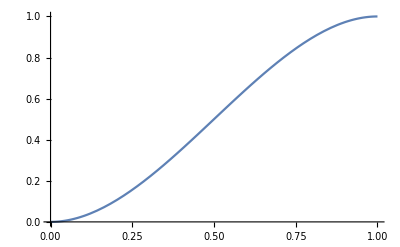

4+4 p+7 p^2+6 p^3-54 p^4+12 p^5+75 p^6-66 p^7+16 p^8

4+4 p+7 p^2+6 p^3-54 p^4+12 p^5+75 p^6-66 p^7+16 p^8

4+4 p+8 p^2+4 p^3-59 p^4+28 p^5+61 p^6-62 p^7+16 p^8

4+4 p+8 p^2+4 p^3-59 p^4+28 p^5+61 p^6-62 p^7+16 p^8

4+4 p+8 p^2+4 p^3-59 p^4+28 p^5+61 p^6-62 p^7+16 p^8

4+4 p+7 p^2+6 p^3-57 p^4+20 p^5+68 p^6-64 p^7+16 p^8

4+4 p+7 p^2+6 p^3-57 p^4+20 p^5+68 p^6-64 p^7+16 p^8

99/16

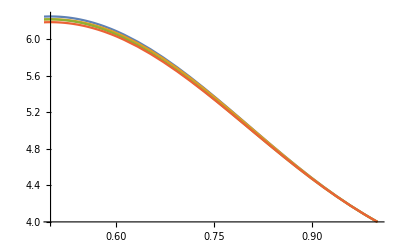

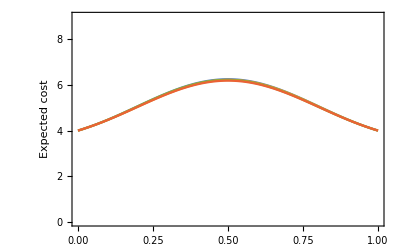

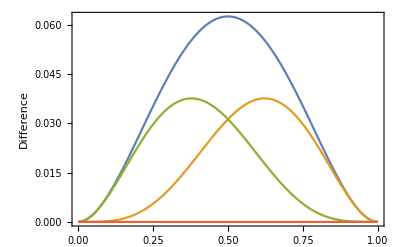

/home/julia/git/ComplexityOfBooleanFunctions/plots/itermajalgs.eps

/home/julia/git/ComplexityOfBooleanFunctions/plots/itermajalgsdiff.eps

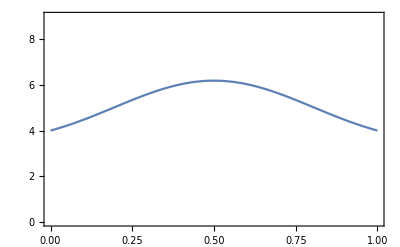

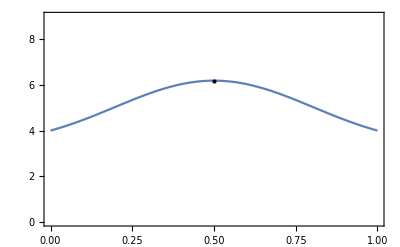

/home/julia/git/ComplexityOfBooleanFunctions/plots/itermajDp.eps

{25/4,{p→1/2}}

{4+4 Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377+7 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^2+6 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^3-54 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^4+12 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^5+75 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^6-66 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^7+16 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^8,{p→Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377}}

{4+4 Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225+8 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^2+4 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^3-59 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^4+28 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^5+61 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^6-62 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^7+16 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^8,{p→Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225}}

{99/16,{p→1/2}}

```mathematica
k = 2;
n = 2k-1;
Pdiff[p_] = 1 - p^k - (1-p)^k;
Plot[Pdiff[p],{p,0,1}]

P1[p_] = Sum[Binomial[n,i]*p^i*(1-p)^(n-i),{i,k,n}];
Plot[P1[p],{p,0,1}]
Palt[p_] = 1 - P1[p]^k - (1-P1[p])^k;
pss[p_]= p*P1[p] + (1-p)(1-P1[p]);

A1[p_]= (2 + Pdiff[p])(2 + Palt[p]);
A4[p_]= 2 + Pdiff[p] + 1 + (pss[p]+P1[p](1-P1[p])(1-p) + (1-P1[p])P1[p]p)*(1 + Pdiff[p]) + ((1-pss[p])+P1[p]p(1-p)^2 + (1-P1[p])(1-p)p^2)*(2 + Pdiff[p]);
A3[p_]= 2 + Pdiff[p] + 1 + (1-P1[p](1-p)+P1[p](1-P1[p])(1-p))*(1 + Pdiff[p]) + (P1[p](1-p) + P1[p]p(1-p)^2+(1-P1[p])p(1-(1-p)^2) + (1-P1[p])(1-p)p^2)*(2 + Pdiff[p]);
A2[p_]=A3[1-p];

A2new[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(1+p+p^2(2+Pdiff[p]))+
(1-P1[p])p(2+Pdiff[p]+P1[p](1+(1-p)))+
P1[p](1-p)(1+p+(1-p^2)(2+Pdiff[p]))+
P1[p]p(1+(1-p)+(1-p)^2(2+Pdiff[p]));
Expand[A2new[p]]
A2hs[p_]=4p^0+4p^1+7p^2+6p^3+-54p^4+12p^5+75p^6+-66p^7+16p^8+0p^9

A3new[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(1+p+p^2(2+Pdiff[p]))+
(1-P1[p])p(1+(1-p)+(1-(1-p)^2)(2+Pdiff[p]))+
P1[p](1-p)(2+Pdiff[p]+(1-P1[p])(1+p))+
P1[p]p(1+(1-p)+(1-p)^2(2+Pdiff[p]));
Expand[A3new[p]]
Expand[A2new[1-p]]
A3hs[p_]=4p^0+4p^1+8p^2+4p^3+-59p^4+28p^5+61p^6+-62p^7+16p^8+0p^9

A4new[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(1+p+p^2(2+Pdiff[p]))+
(1-P1[p])p(2+Pdiff[p]+P1[p](1+(1-p)))+
P1[p](1-p)(2+Pdiff[p]+(1-P1[p])(1+p))+
P1[p]p(1+(1-p)+(1-p)^2(2+Pdiff[p]));
Expand[A4new[p]]
A4hs[p_]=4p^0+4p^1+7p^2+6p^3+-57p^4+20p^5+68p^6+-64p^7+16p^8+0p^9
A4hs[1/2]
Plot[{A1[p],A2new[p],A3new[p],A4new[p]},{p,0,1},PlotLegends->{MaTeX@{"\mathbb{E}_x^{\pi_p}[c(A_1,x)]","\mathbb{E}_x^{\pi_p}[c(A_2,x)]","\mathbb{E}_x^{\pi_p}[c(A_3,x)]","\mathbb{E}_x^{\pi_p}[c(A_4,x)]"}}, PlotRange->{{0.5,1},{4.0,6.25}}]
plot = Plot[{A1[p],A2new[p],A3new[p],A4new[p]},{p,0,1},PlotLegends->{MaTeX@{"\mathbb{E}_x^{\pi_p}[c(A_1,x)]","\mathbb{E}_x^{\pi_p}[c(A_2,x)]","\mathbb{E}_x^{\pi_p}[c(A_3,x)]","\mathbb{E}_x^{\pi_p}[c(A_4,x)]"}}, Frame -> True,FrameLabel->{MaTeX@"p", "Expected cost"},LabelStyle->{Black,Medium},PlotRange->{{0,1},{0,9}}]
diffplot = Plot[{A1[p]-A4new[p],A2new[p]-A4new[p],A3new[p]-A4new[p],A4new[p]-A4new[p]},{p,0,1},PlotLegends->{MaTeX@{"\mathbb{E}_x^{\pi_p}[c(A_1,x)]-\mathbb{E}_x^{\pi_p}[c(A_4,x)]","\mathbb{E}_x^{\pi_p}[c(A_2,x)]-\mathbb{E}_x^{\pi_p}[c(A_4,x)]","\mathbb{E}_x^{\pi_p}[c(A_3,x)]-\mathbb{E}_x^{\pi_p}[c(A_4,x)]","\mathbb{E}_x^{\pi_p}[c(A_4,x)]-\mathbb{E}_x^{\pi_p}[c(A_4,x)]"}},Frame -> True,FrameLabel->{MaTeX@"p", "Difference"},LabelStyle->{Black,Medium} ,PlotRange->Full]
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/itermajalgs.eps",plot]
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/itermajalgsdiff.eps",diffplot]
plotDp = Plot[A4new[p],{p,0,1},Frame -> True,FrameLabel->{MaTeX@"p", MaTeX@"D_p(f)"},LabelStyle->{Black,Medium} ,PlotRange->{{0,1},{0,9}}]
plotDp = Show[plotDp,Epilog->{PointSize->Large,Point[{{0.5,6.1875}}]}]
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/itermajDp.eps",plotDp]
Maximize[{A1[p],0<p<1},p]
Maximize[{A2new[p],0<p<1},p]
Maximize[{A3new[p],0<p<1},p]
Maximize[{A4new[p],0<p<1},p]
```

-Graphics-

-Graphics-

4+4 p+7 p^2+6 p^3-54 p^4+12 p^5+75 p^6-66 p^7+16 p^8

4+4 p+7 p^2+6 p^3-54 p^4+12 p^5+75 p^6-66 p^7+16 p^8

4+4 p+8 p^2+4 p^3-59 p^4+28 p^5+61 p^6-62 p^7+16 p^8

4+4 p+8 p^2+4 p^3-59 p^4+28 p^5+61 p^6-62 p^7+16 p^8

4+4 p+8 p^2+4 p^3-59 p^4+28 p^5+61 p^6-62 p^7+16 p^8

4+4 p+7 p^2+6 p^3-57 p^4+20 p^5+68 p^6-64 p^7+16 p^8

4+4 p+7 p^2+6 p^3-57 p^4+20 p^5+68 p^6-64 p^7+16 p^8

99/16

-Graphics-

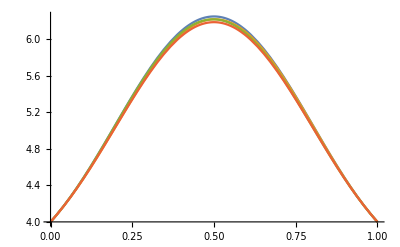

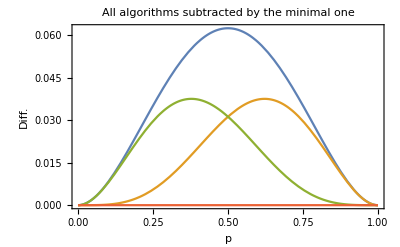

/home/julia/git/ComplexityOfBooleanFunctions/plots/itermajalgs.eps

/home/julia/git/ComplexityOfBooleanFunctions/plots/itermajalgsdiff.eps

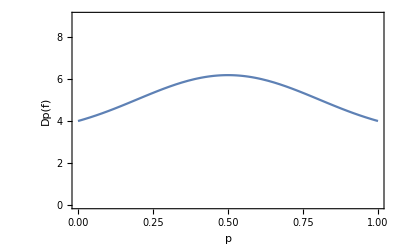

{25/4,{p→1/2}}

{4+4 Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377+7 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^2+6 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^3-54 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^4+12 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^5+75 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^6-66 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^7+16 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^8,{p→Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377}}

{4+4 Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225+8 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^2+4 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^3-59 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^4+28 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^5+61 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^6-62 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^7+16 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^8,{p→Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225}}

{99/16,{p→1/2}}

5+4 p+2 p^2+8 p^3-38 p^4-4 p^5+76 p^6-64 p^7+16 p^8

4+4 p+7 p^2+6 p^3-45 p^4+79 p^6-66 p^7+16 p^8

5+4 p+3 p^2+6 p^3-40 p^4+4 p^5+69 p^6-62 p^7+16 p^8

5+4 p+2 p^2+8 p^3-35 p^4-12 p^5+83 p^6-66 p^7+16 p^8

5+4 p+2 p^2+8 p^3-50 p^4+16 p^5+65 p^6-62 p^7+16 p^8

5+4 p+2 p^2+8 p^3-47 p^4+8 p^5+72 p^6-64 p^7+16 p^8

5+4 p+3 p^2+6 p^3-52 p^4+24 p^5+58 p^6-60 p^7+16 p^8

5+4 p+3 p^2+6 p^3-37 p^4-4 p^5+76 p^6-64 p^7+16 p^8

4+4 p+7 p^2+6 p^3-42 p^4-8 p^5+86 p^6-68 p^7+16 p^8

4+4 p+8 p^2+4 p^3-47 p^4+8 p^5+72 p^6-64 p^7+16 p^8

5+4 p+3 p^2+6 p^3-49 p^4+16 p^5+65 p^6-62 p^7+16 p^8

4+4 p+8 p^2+4 p^3-44 p^4+79 p^6-66 p^7+16 p^8

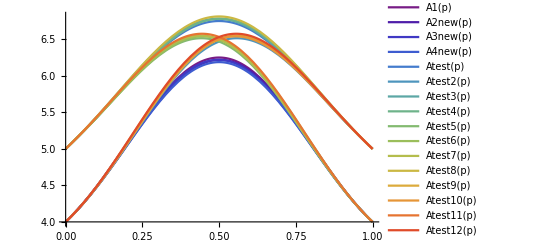

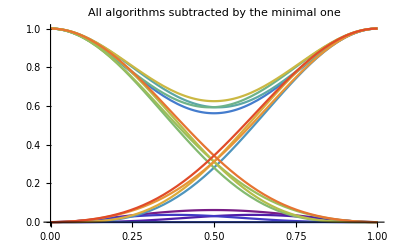

{}

{}

{}

4+4 p+8 p^2+4 p^3-56 p^4+20 p^5+68 p^6-64 p^7+16 p^8

25/4

4+5 p+4 p^2+2 p^3-32 p^4-3 p^5+44 p^6-8 p^7-20 p^8+8 p^9

4+4 p+8 p^2+4 p^3-59 p^4+19 p^5+100 p^6-120 p^7+52 p^8-8 p^9

4+5 p+4 p^2+2 p^3-35 p^4-4 p^5+76 p^6-64 p^7+16 p^8

99/16

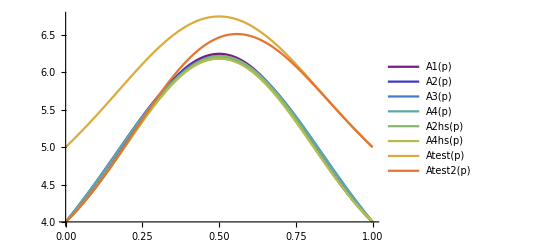

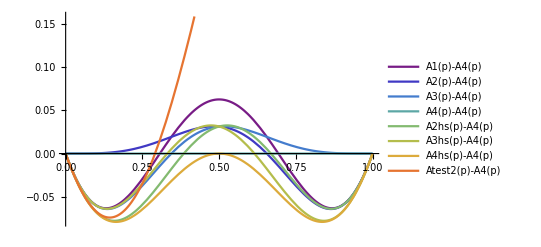

4+4 eps+8 eps^2+4 eps^3-56 eps^4+20 eps^5+68 eps^6-64 eps^7+16 eps^8

4+4 eps+8 eps^2+4 eps^3-59 eps^4+19 eps^5+100 eps^6-120 eps^7+52 eps^8-8 eps^9

4+5 eps+4 eps^2+2 eps^3-32 eps^4-3 eps^5+44 eps^6-8 eps^7-20 eps^8+8 eps^9

4+5 eps+4 eps^2+2 eps^3-35 eps^4-4 eps^5+76 eps^6-64 eps^7+16 eps^8

{{p→0.344446}}

{4.001}

{4.35897}

{{p→0.655554}}

{-4.001}

{-4.35897}

{{p→0.344446},{p→1.},{p→1.},{p→1.},{p→1.}}

4+4 eps+8 eps^2+4 eps^3-56 eps^4+20 eps^5+68 eps^6-64 eps^7+16 eps^8

4+4 eps+8 eps^2+4 eps^3-59 eps^4+19 eps^5+100 eps^6-120 eps^7+52 eps^8-8 eps^9

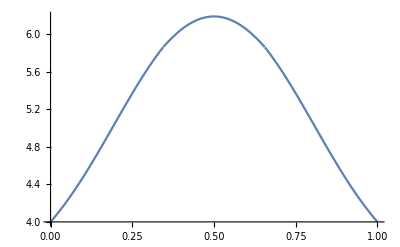

```mathematica
Atest[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(2+Pdiff[p]+P1[p](1+p))+
(1-P1[p])p(2+Pdiff[p]+P1[p](1+(1-p)))+
P1[p](1-p)(2+Pdiff[p]+(1-P1[p])(1+p))+
P1[p]p(2+Pdiff[p]+(1-P1[p])(1+(1-p)));
Expand[Atest[p]]

Atest2[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(1+p+p^2(2+Pdiff[p]))+
(1-P1[p])p(2+Pdiff[p]+P1[p](1+(1-p)))+
P1[p](1-p)(2+Pdiff[p]+(1-P1[p])(1+p))+
P1[p]p(2+Pdiff[p]+(1-P1[p])(1+(1-p)));
Expand[Atest2[p]]

Atest3[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(2+Pdiff[p]+P1[p](1+p))+
(1-P1[p])p(1+(1-p)+(1-(1-p)^2)(2+Pdiff[p]))+
P1[p](1-p)(2+Pdiff[p]+(1-P1[p])(1+p))+
P1[p]p(2+Pdiff[p]+(1-P1[p])(1+(1-p)));
Expand[Atest3[p]]

Atest4[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(2+Pdiff[p]+P1[p](1+p))+
(1-P1[p])p(2+Pdiff[p]+P1[p](1+(1-p)))+
P1[p](1-p)(1+p+(1-p^2)(2+Pdiff[p]))+
P1[p]p(2+Pdiff[p]+(1-P1[p])(1+(1-p)));
Expand[Atest4[p]]

Atest5[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(2+Pdiff[p]+P1[p](1+p))+
(1-P1[p])p(2+Pdiff[p]+P1[p](1+(1-p)))+
P1[p](1-p)(2+Pdiff[p]+(1-P1[p])(1+p))+
P1[p]p(1+(1-p)+(1-p)^2(2+Pdiff[p]));
Expand[Atest5[p]]

Atest6[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(2+Pdiff[p]+P1[p](1+p))+
(1-P1[p])p(2+Pdiff[p]+P1[p](1+(1-p)))+
P1[p](1-p)(1+p+(1-p^2)(2+Pdiff[p]))+
P1[p]p(1+(1-p)+(1-p)^2(2+Pdiff[p]));
Expand[Atest6[p]]

Atest7[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(2+Pdiff[p]+P1[p](1+p))+
(1-P1[p])p(1+(1-p)+(1-(1-p)^2)(2+Pdiff[p]))+
P1[p](1-p)(2+Pdiff[p]+(1-P1[p])(1+p))+
P1[p]p(1+(1-p)+(1-p)^2(2+Pdiff[p]));
Expand[Atest7[p]]

Atest8[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(2+Pdiff[p]+P1[p](1+p))+
(1-P1[p])p(1+(1-p)+(1-(1-p)^2)(2+Pdiff[p]))+
P1[p](1-p)(1+p+(1-p^2)(2+Pdiff[p]))+
P1[p]p(2+Pdiff[p]+(1-P1[p])(1+(1-p)));
Expand[Atest8[p]]

Atest9[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(1+p+p^2(2+Pdiff[p]))+
(1-P1[p])p(2+Pdiff[p]+P1[p](1+(1-p)))+
P1[p](1-p)(1+p+(1-p^2)(2+Pdiff[p]))+
P1[p]p(2+Pdiff[p]+(1-P1[p])(1+(1-p)));
Expand[Atest9[p]]

Atest10[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(1+p+p^2(2+Pdiff[p]))+
(1-P1[p])p(1+(1-p)+(1-(1-p)^2)(2+Pdiff[p]))+
P1[p](1-p)(2+Pdiff[p]+(1-P1[p])(1+p))+
P1[p]p(2+Pdiff[p]+(1-P1[p])(1+(1-p)));
Expand[Atest10[p]]

Atest11[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(2+Pdiff[p]+P1[p](1+p))+
(1-P1[p])p(1+(1-p)+(1-(1-p)^2)(2+Pdiff[p]))+
P1[p](1-p)(1+p+(1-p^2)(2+Pdiff[p]))+
P1[p]p(1+(1-p)+(1-p)^2(2+Pdiff[p]));
Expand[Atest11[p]]

Atest12[p_]=2 + Pdiff[p] + 1 +
(1-P1[p])(1-p)(1+p+p^2(2+Pdiff[p]))+
(1-P1[p])p(1+(1-p)+(1-(1-p)^2)(2+Pdiff[p]))+
P1[p](1-p)(1+p+(1-p^2)(2+Pdiff[p]))+
P1[p]p(2+Pdiff[p]+(1-P1[p])(1+(1-p)));
Expand[Atest12[p]]

b={A1[p],A2new[p],A3new[p],A4new[p],Atest[p],Atest2[p],Atest3[p],Atest4[p],Atest5[p],Atest6[p],Atest7[p],Atest8[p],Atest9[p],Atest10[p],Atest11[p],Atest12[p]};
Plot[{A1[p],A2new[p],A3new[p],A4new[p],Atest[p],Atest2[p],Atest3[p],Atest4[p],Atest5[p],Atest6[p],Atest7[p],Atest8[p],Atest9[p],Atest10[p],Atest11[p],Atest12[p]},{p,0,1},PlotStyle->ColorData["Rainbow"]/@(Range[0,Length@b]/Length@b), PlotLegends->"Expressions"]

c=Subtract[{A1[p],A2new[p],A3new[p],A4new[p],Atest[p],Atest2[p],Atest3[p],Atest4[p],Atest5[p],Atest6[p],Atest7[p],Atest8[p],Atest9[p],Atest10[p],Atest11[p],Atest12[p]},A4hs[p]];
Plot[c,{p,0,1},PlotStyle->ColorData["Rainbow"]/@(Range[0,Length@c]/Length@c),PlotLabel->"All algorithms subtracted by the minimal one"]

NSolve[Atest2[p]==A4hs[p]&&p<1&&p>0]
NSolve[Atest10[p]==A4hs[p]&&p<1&&p>0]
NSolve[A3hs[p]==A4hs[p]&&p<1&&p>0]

Expand[A1[p]]
A1[1/2]
Expand[A2[p]]
Expand[A3[p]]
Expand[A4[p]]
A4[1/2]
d={A1[p],A2[p],A3[p],A4[p],A2hs[p],A4hs[p],Atest[p],Atest2[p]};
Plot[{A1[p],A2[p],A3[p],A4[p],A2hs[p],A4hs[p],Atest[p],Atest2[p]},{p,0,1},PlotStyle->ColorData["Rainbow"]/@(Range[0,Length@d]/Length@d), PlotLegends->"Expressions"]
e = {A1[p]-A4[p],A2[p]-A4[p],A3[p]-A4[p],A4[p]-A4[p],A2hs[p]-A4[p],A3hs[p]-A4[p],A4hs[p]-A4[p],Atest2[p]-A4[p]};
Plot[{A1[p]-A4[p],A2[p]-A4[p],A3[p]-A4[p],A4[p]-A4[p],A2hs[p]-A4[p],A3hs[p]-A4[p],A4hs[p]-A4[p],Atest2[p]-A4[p]},{p,0,1}, PlotStyle->ColorData["Rainbow"]/@(Range[0,Length@e]/Length@e),PlotLegends -> "Expressions"]
Expand[A1[1-eps]]
Expand[A2[1-eps]]
Expand[A3[1-eps]]
Expand[A4[1-eps]]

intersect1 = NSolve[A3[p]==A4[p]&&p<1&&p>0]
A4'[p/.intersect1]
A3'[p/.intersect1]
intersect2 = NSolve[A2[p]==A4[p]&&p<1&&p>0]
A4'[p/.intersect2]
A2'[p/.intersect2]

intersect3 = NSolve[A2[p]==A1[p]&&p<=1&&p>0]
Expand[A1[eps]]
Expand[A3[eps]]

Plot[Min[A3[p],A2[p],A4[p]],{p,0,1}]
```

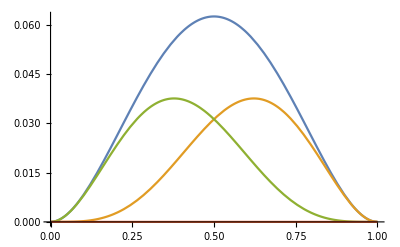

{25/4,{p→1/2}}

{4+4 Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377+7 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^2+6 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^3-54 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^4+12 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^5+75 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^6-66 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^7+16 (Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377)^8,{p→Root0.503Root[2+7 #1+9 #1^2-108 #1^3+30 #1^4+225 #1^5-231 #1^6+64 #1^7&,2]0.5029291046687377}}

{4+4 Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225+8 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^2+4 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^3-59 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^4+28 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^5+61 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^6-62 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^7+16 (Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225)^8,{p→Root0.497Root[2+8 #1+6 #1^2-118 #1^3+70 #1^4+183 #1^5-217 #1^6+64 #1^7&,2]0.49707089533126225}}

{99/16,{p→1/2}}

5+4 p+2 p^2+8 p^3-38 p^4-4 p^5+76 p^6-64 p^7+16 p^8

4+4 p+7 p^2+6 p^3-45 p^4+79 p^6-66 p^7+16 p^8

5+4 p+3 p^2+6 p^3-40 p^4+4 p^5+69 p^6-62 p^7+16 p^8

5+4 p+2 p^2+8 p^3-35 p^4-12 p^5+83 p^6-66 p^7+16 p^8

5+4 p+2 p^2+8 p^3-50 p^4+16 p^5+65 p^6-62 p^7+16 p^8

5+4 p+2 p^2+8 p^3-47 p^4+8 p^5+72 p^6-64 p^7+16 p^8

5+4 p+3 p^2+6 p^3-52 p^4+24 p^5+58 p^6-60 p^7+16 p^8

5+4 p+3 p^2+6 p^3-37 p^4-4 p^5+76 p^6-64 p^7+16 p^8

4+4 p+7 p^2+6 p^3-42 p^4-8 p^5+86 p^6-68 p^7+16 p^8

4+4 p+8 p^2+4 p^3-47 p^4+8 p^5+72 p^6-64 p^7+16 p^8

5+4 p+3 p^2+6 p^3-49 p^4+16 p^5+65 p^6-62 p^7+16 p^8

4+4 p+8 p^2+4 p^3-44 p^4+79 p^6-66 p^7+16 p^8

-Graphics-

-Graphics-

{}

{}

{}

4+4 p+8 p^2+4 p^3-56 p^4+20 p^5+68 p^6-64 p^7+16 p^8

25/4

4+5 p+4 p^2+2 p^3-32 p^4-3 p^5+44 p^6-8 p^7-20 p^8+8 p^9

4+4 p+8 p^2+4 p^3-59 p^4+19 p^5+100 p^6-120 p^7+52 p^8-8 p^9

4+5 p+4 p^2+2 p^3-35 p^4-4 p^5+76 p^6-64 p^7+16 p^8

99/16

-Graphics-

-Graphics-

4+4 eps+8 eps^2+4 eps^3-56 eps^4+20 eps^5+68 eps^6-64 eps^7+16 eps^8

4+4 eps+8 eps^2+4 eps^3-59 eps^4+19 eps^5+100 eps^6-120 eps^7+52 eps^8-8 eps^9

4+5 eps+4 eps^2+2 eps^3-32 eps^4-3 eps^5+44 eps^6-8 eps^7-20 eps^8+8 eps^9

4+5 eps+4 eps^2+2 eps^3-35 eps^4-4 eps^5+76 eps^6-64 eps^7+16 eps^8

{{p→0.344446}}

{4.001}

{4.35897}

{{p→0.655554}}

{-4.001}

{-4.35897}

{{p→0.344446},{p→1.},{p→1.},{p→1.},{p→1.}}

4+4 eps+8 eps^2+4 eps^3-56 eps^4+20 eps^5+68 eps^6-64 eps^7+16 eps^8

4+4 eps+8 eps^2+4 eps^3-59 eps^4+19 eps^5+100 eps^6-120 eps^7+52 eps^8-8 eps^9

-Graphics-

```mathematica
"interactive plot"%716DynamicModule[{xc,dx},Manipulate[Plot[{A1[p],A2[p],A3[p],A4[p],A2hs[p],A4hs[p],Atest[p],Atest2[p]},{p,xc-dx,xc+dx},PlotStyle->ColorData["Rainbow"]/@(Range[0,Length[d]]/Length[d]),PlotLegends->"Expressions"],{{xc,1/2,"center"},-5/2,7/2},{{dx,0.5,"zoom"},3,0.03}],DynamicModuleValues:>{}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.